```mathematica
Needs["GroupTheory`"]
```

DirectoryQ::badfile: The specified argument GroupTheory`Auxiliary`Private`dest$18477 should be a valid string or File.

## Crystal field expansion for cubic group O_h

```mathematica
Ohgroup=GTInstallGroup[Oh,GOVerbose->"False"];
```

```mathematica
vcr=GTCrystalField[Ohgroup,6]
```

A[0,0] Y[0,0]+r^4 A[4,4] Y[4,-4]+√(14/5) r^4 A[4,4] Y[4,0]+r^4 A[4,4] Y[4,4]+r^6 A[6,4] Y[6,-4]-√(2/7) r^6 A[6,4] Y[6,0]+r^6 A[6,4] Y[6,4]

### Test some things and get familiar with the GT operators

Test that the BST operators (Buckmaster-Smith-Thornley) correspond to the (C^(l))_m operators of the more recent review of Kuzmin and Tishin (2008). 
We compare matrix elements of the BST operators to Equations () in the review.

```mathematica
jVal=4;
mVal=2;
mValp=3;
```

```mathematica
GTBSTOperatorElement[2,1,jVal,mValp,mVal]
```

-(5 √21)/2

```mathematica
1/2*(3*mVal^2-jVal*(jVal+1))*KroneckerDelta[mVal,mValp]
```

0

```mathematica
-(mVal+mValp)*(3/8*(jVal+mValp)*(jVal-mVal))^(1/2)*KroneckerDelta[mValp,mVal+1]
```

-(5 √21)/2

```mathematica
GTBSTOperator[0,0,4];
%//MatrixForm

GTBSTOperator[4,-4,4];
%//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(0 | 0 | 0 | 0 | 105 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 105 √(5/2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 45 √(35/2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 105 √(5/2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 105
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
GTBSTOperator[2,2,2];
%//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0
0 | 3 √(3/2) | 0 | 0 | 0
0 | 0 | 3 | 0 | 0)

### Crystal field expansion in terms of BST or Stevens operators, starting from the expression in terms of the Y[l,m]

Let’s go from BST to Stevens operators using equations on page 25 of Danielsen and Lindgard paper. 
Choose J=4, m=2 for concreteness.

```mathematica
JVal=4;
lVal=2;
mVal=2;
```

```mathematica
KCoeff[2,2]=1/4*Sqrt[15/Pi];
KCoeff[2,0]=1/4*Sqrt[5/Pi];
KCoeff[4,4]=3/16*Sqrt[35/Pi];
KCoeff[4,0]=1/16*Sqrt[9/Pi];
KCoeff[6,4]=3/32*Sqrt[91/Pi];
KCoeff[6,0]=1/32*Sqrt[13/Pi];
```

The DL transformation (5.1) on page 25 (with K[l,m] = normalizing coefficients in the tesseral harmonic from page DL 52) relates GTBSTOperator[l,m,J] to GTStevensOperator[l,m,J]:

```mathematica
temp1=If[mVal==0,1/KCoeff[lVal,mVal]*Sqrt[(2*lVal+1)/(4*Pi)]*GTBSTOperator[lVal,0,JVal], 1/KCoeff[lVal,mVal]*Sqrt[(2*lVal+1)/(4*Pi)/2]*(GTBSTOperator[lVal,-mVal,JVal]+(-1)^mVal*GTBSTOperator[lVal,mVal,JVal])];
%//MatrixForm
```

(0 | 0 | 2 √7 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 √7 | 0 | 0 | 0 | 0 | 0
2 √7 | 0 | 0 | 0 | 3 √10 | 0 | 0 | 0 | 0
0 | 3 √7 | 0 | 0 | 0 | 10 | 0 | 0 | 0
0 | 0 | 3 √10 | 0 | 0 | 0 | 3 √10 | 0 | 0
0 | 0 | 0 | 10 | 0 | 0 | 0 | 3 √7 | 0
0 | 0 | 0 | 0 | 3 √10 | 0 | 0 | 0 | 2 √7
0 | 0 | 0 | 0 | 0 | 3 √7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 √7 | 0 | 0)

```mathematica
GTStevensOperator[lVal,mVal,JVal]//MatrixForm
```

(0 | 0 | 2 √7 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 √7 | 0 | 0 | 0 | 0 | 0
2 √7 | 0 | 0 | 0 | 3 √10 | 0 | 0 | 0 | 0
0 | 3 √7 | 0 | 0 | 0 | 10 | 0 | 0 | 0
0 | 0 | 3 √10 | 0 | 0 | 0 | 3 √10 | 0 | 0
0 | 0 | 0 | 10 | 0 | 0 | 0 | 3 √7 | 0
0 | 0 | 0 | 0 | 3 √10 | 0 | 0 | 0 | 2 √7
0 | 0 | 0 | 0 | 0 | 3 √7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 √7 | 0 | 0)

Stevens operators defined via BST operators in Eq.5.1 on page 25 in Danielsen and Lindgard and  GTStevensOperator[l,m,J] are identical.

```mathematica
temp1-GTStevensOperator[lVal,mVal,JVal]
%//Total[Abs[#],{1,2}]&
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

0

What about the difference operators O[l,m](s) in Danielsen and Lindgard. It contains I and is antisymmetric. 
I am not sure I need these for the expansion of the crystal field Hamiltonian. Let’s assume for now that this is done only in terms of the c combination above (as it agrees with GTStevensOperator that may be correct).

```mathematica
1/KCoeff[lVal,mVal]*I*Sqrt[(2*lVal+1)/(4*Pi)/2]*(GTBSTOperator[lVal,-mVal,JVal]-(-1)^mVal*GTBSTOperator[lVal,mVal,JVal]);
%//MatrixForm
```

(0 | 0 | 2 ⅈ √7 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 ⅈ √7 | 0 | 0 | 0 | 0 | 0
-2 ⅈ √7 | 0 | 0 | 0 | 3 ⅈ √10 | 0 | 0 | 0 | 0
0 | -3 ⅈ √7 | 0 | 0 | 0 | 10 ⅈ | 0 | 0 | 0
0 | 0 | -3 ⅈ √10 | 0 | 0 | 0 | 3 ⅈ √10 | 0 | 0
0 | 0 | 0 | -10 ⅈ | 0 | 0 | 0 | 3 ⅈ √7 | 0
0 | 0 | 0 | 0 | -3 ⅈ √10 | 0 | 0 | 0 | 2 ⅈ √7
0 | 0 | 0 | 0 | 0 | -3 ⅈ √7 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ √7 | 0 | 0)

Compare to Stevens operators defined in Lea, Leask and Wolf paper, focusing on J=4 for concreteness. 
From the comparison of the spectrum, we know that O[l,m] in their paper are identical to GTStevensOperator[l,m,J=4]. 
Let’s see whether we obtain the same expansion of the crystal field Hamiltonian with factors F[4] = 60 and F[6] = 1260 as well as the relative factors in O[4]=O[4,0] + 5.0*O[4,4] and O[6] = O[6,0] - 21.0*O[6,4].

```mathematica
JVal=4;
```

Expand the crystal field for O_h in Y_lm. Then replace Y_lmby Wybourne operators C_lm using that Y_lm→√((2l+1)/(4π))C_lm. Then replace the C_lm by the combination of Stevens’ operators given in Danielsen and Lindgard (DL), which includes the K_lm coefficients given on p.56 in DL. The resulting Hamiltonian is identical to Lea et al. To show this, one can factor out the greatest common divisor of all the matrix elements as shown below.

```mathematica
vcr=GTCrystalField[Ohgroup,6]//FullSimplify
temp=vcr//.{Y[ll_,mm_]->Sqrt[(2*ll+1)/4/Pi]*YY[ll,mm]};
temp=temp//.{YY[ll_,mm_]->Y[ll,mm]};
vcrSt=temp//.{r->1,Y[4,-4]->KCoeff[4,4]*Sqrt[8*Pi/9]*OSt[4,4]-Y[4,4],Y[4,0]->KCoeff[4,0]*Sqrt[4*Pi/9]*OSt[4,0],Y[6,-4]->KCoeff[6,4]*Sqrt[8*Pi/13]*OSt[6,4]-Y[6,4],Y[6,0]->KCoeff[6,0]*Sqrt[4*Pi/13]*OSt[6,0]}//FullSimplify
```

A[0,0] Y[0,0]+1/5 r^4 A[4,4] (5 Y[4,-4]+√70 Y[4,0]+5 Y[4,4])+1/7 r^6 A[6,4] (7 Y[6,-4]-√14 Y[6,0]+7 Y[6,4])

(42 √70 A[4,4] (OSt[4,0]+5 OSt[4,4])-5 √182 A[6,4] (OSt[6,0]-21 OSt[6,4])+560 A[0,0] Y[0,0])/(1120 √π)

```mathematica
42*Sqrt[70]*60/5/Sqrt[182]/1260
```

2/(√65)

```mathematica
GTStevensTheta["Pr",4]

GTStevensTheta["Pr",6]
```

-4/5445

272/4459455

```mathematica
GTStevensTheta["Pr",4]*Sqrt[4*Pi/9]*(KCoeff[4,0]*A[4,4]*GTStevensOperator[4,0,JVal]+KCoeff[4,4]*A[4,4]*GTStevensOperator[4,4,JVal]);
%//MatrixForm
```

(-28/363 A[4,4] | 0 | 0 | 0 | -14/363 √2 A[4,4] | 0 | 0 | 0 | 0
0 | 14/121 A[4,4] | 0 | 0 | 0 | -14/363 √5 A[4,4] | 0 | 0 | 0
0 | 0 | 2/33 A[4,4] | 0 | 0 | 0 | -2/121 √35 A[4,4] | 0 | 0
0 | 0 | 0 | -6/121 A[4,4] | 0 | 0 | 0 | -14/363 √5 A[4,4] | 0
-14/363 √2 A[4,4] | 0 | 0 | 0 | -12/121 A[4,4] | 0 | 0 | 0 | -14/363 √2 A[4,4]
0 | -14/363 √5 A[4,4] | 0 | 0 | 0 | -6/121 A[4,4] | 0 | 0 | 0
0 | 0 | -2/121 √35 A[4,4] | 0 | 0 | 0 | 2/33 A[4,4] | 0 | 0
0 | 0 | 0 | -14/363 √5 A[4,4] | 0 | 0 | 0 | 14/121 A[4,4] | 0
0 | 0 | 0 | 0 | -14/363 √2 A[4,4] | 0 | 0 | 0 | -28/363 A[4,4])

The relative numbers between OSt[4,0] and OSt[4,4] as well as between OSt[6,0] and OSt[6,4] are correct. The common factors F[4] and F[6] follow immediately from just looking at the matrices of O[4] and O[6] and dividing by the largest common factor of all (diagonal ) entries in the matrix.

```mathematica
temp=GTStevensOperator[4,0,JVal]+5*GTStevensOperator[4,4,JVal];
%//MatrixForm
%%/60//MatrixForm
```

(840 | 0 | 0 | 0 | 60 √70 | 0 | 0 | 0 | 0
0 | -1260 | 0 | 0 | 0 | 300 √7 | 0 | 0 | 0
0 | 0 | -660 | 0 | 0 | 0 | 900 | 0 | 0
0 | 0 | 0 | 540 | 0 | 0 | 0 | 300 √7 | 0
60 √70 | 0 | 0 | 0 | 1080 | 0 | 0 | 0 | 60 √70
0 | 300 √7 | 0 | 0 | 0 | 540 | 0 | 0 | 0
0 | 0 | 900 | 0 | 0 | 0 | -660 | 0 | 0
0 | 0 | 0 | 300 √7 | 0 | 0 | 0 | -1260 | 0
0 | 0 | 0 | 0 | 60 √70 | 0 | 0 | 0 | 840)

(14 | 0 | 0 | 0 | √70 | 0 | 0 | 0 | 0
0 | -21 | 0 | 0 | 0 | 5 √7 | 0 | 0 | 0
0 | 0 | -11 | 0 | 0 | 0 | 15 | 0 | 0
0 | 0 | 0 | 9 | 0 | 0 | 0 | 5 √7 | 0
√70 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | √70
0 | 5 √7 | 0 | 0 | 0 | 9 | 0 | 0 | 0
0 | 0 | 15 | 0 | 0 | 0 | -11 | 0 | 0
0 | 0 | 0 | 5 √7 | 0 | 0 | 0 | -21 | 0
0 | 0 | 0 | 0 | √70 | 0 | 0 | 0 | 14)

```mathematica
GTStevensOperator[6,0,JVal]-21*GTStevensOperator[6,4,JVal];
%//MatrixForm
%%/1260//MatrixForm
```

(5040 | 0 | 0 | 0 | -7560 √70 | 0 | 0 | 0 | 0
0 | -21420 | 0 | 0 | 0 | 3780 √7 | 0 | 0 | 0
0 | 0 | 27720 | 0 | 0 | 0 | 52920 | 0 | 0
0 | 0 | 0 | 1260 | 0 | 0 | 0 | 3780 √7 | 0
-7560 √70 | 0 | 0 | 0 | -25200 | 0 | 0 | 0 | -7560 √70
0 | 3780 √7 | 0 | 0 | 0 | 1260 | 0 | 0 | 0
0 | 0 | 52920 | 0 | 0 | 0 | 27720 | 0 | 0
0 | 0 | 0 | 3780 √7 | 0 | 0 | 0 | -21420 | 0
0 | 0 | 0 | 0 | -7560 √70 | 0 | 0 | 0 | 5040)

(4 | 0 | 0 | 0 | -6 √70 | 0 | 0 | 0 | 0
0 | -17 | 0 | 0 | 0 | 3 √7 | 0 | 0 | 0
0 | 0 | 22 | 0 | 0 | 0 | 42 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 √7 | 0
-6 √70 | 0 | 0 | 0 | -20 | 0 | 0 | 0 | -6 √70
0 | 3 √7 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 42 | 0 | 0 | 0 | 22 | 0 | 0
0 | 0 | 0 | 3 √7 | 0 | 0 | 0 | -17 | 0
0 | 0 | 0 | 0 | -6 √70 | 0 | 0 | 0 | 4)

One can find F[4] and F[6] (at least in this case) by looking at the greatest common divisor (GCD) of the diagonal entries of O[4] and O[6], respectively.

```mathematica
temp=GTStevensOperator[4,0,JVal]+5*GTStevensOperator[4,4,JVal];
temp=Table[temp[[i,i]],{i,1,Length[temp]}];
GCD[Abs[temp[[1]]],Abs[temp[[2]]],Abs[temp[[3]]],Abs[temp[[4]]],Abs[temp[[5]]],Abs[temp[[6]]],Abs[temp[[7]]],Abs[temp[[8]]],Abs[temp[[9]]]]
temp=GTStevensOperator[6,0,JVal]-21*GTStevensOperator[6,4,JVal];
temp=Table[temp[[i,i]],{i,1,Length[temp]}];
GCD[Abs[temp[[1]]],Abs[temp[[2]]],Abs[temp[[3]]],Abs[temp[[4]]],Abs[temp[[5]]],Abs[temp[[6]]],Abs[temp[[7]]],Abs[temp[[8]]],Abs[temp[[9]]]]
```

60

1260

Conclusion: we can get the crystal field Hamiltonian from first expanding the crystal field expression in terms of Y[l,m] using GTCrystalField[Ohgroup,6]. Then, we replace the Y[l,m] by the GTBSTOperators[l,m,J]. If we want to work with Stevens’ operators instead, we can use the formula in Danielsen and Lindgard to relate the BST operators to the Stevens’ operators and replace the Y[l,m] combinations by the Stevens’ operators, i.e, as done by hand above. This requires the use of the KCoeff[l,m] from the table on p.56 of Danielsen and Lindgard.

```mathematica
temp=vcrSt;
temp=temp/.{A[0,0]->0};
vcrStMatrix=temp/.{OSt[4,0]->GTStevensOperator[4,0,JVal]/60,OSt[4,4]->5*GTStevensOperator[4,4,JVal]/60,OSt[6,0]->GTStevensOperator[6,0,JVal]/1260,OSt[6,4]->GTStevensOperator[6,4,JVal]/1260};
%//MatrixForm
```

((588 √70 A[4,4]-20 √182 A[6,4])/(1120 √π) | 0 | 0 | 0 | (14700 A[4,4]+420 √65 A[6,4])/(1120 √π) | 0 | 0 | 0 | 0
0 | (-882 √70 A[4,4]+85 √182 A[6,4])/(1120 √π) | 0 | 0 | 0 | (7350 √10 A[4,4]-105 √26 A[6,4])/(1120 √π) | 0 | 0 | 0
0 | 0 | (-462 √70 A[4,4]-110 √182 A[6,4])/(1120 √π) | 0 | 0 | 0 | (3150 √70 A[4,4]-210 √182 A[6,4])/(1120 √π) | 0 | 0
0 | 0 | 0 | (378 √70 A[4,4]-5 √182 A[6,4])/(1120 √π) | 0 | 0 | 0 | (7350 √10 A[4,4]-105 √26 A[6,4])/(1120 √π) | 0
(14700 A[4,4]+420 √65 A[6,4])/(1120 √π) | 0 | 0 | 0 | (756 √70 A[4,4]+100 √182 A[6,4])/(1120 √π) | 0 | 0 | 0 | (14700 A[4,4]+420 √65 A[6,4])/(1120 √π)
0 | (7350 √10 A[4,4]-105 √26 A[6,4])/(1120 √π) | 0 | 0 | 0 | (378 √70 A[4,4]-5 √182 A[6,4])/(1120 √π) | 0 | 0 | 0
0 | 0 | (3150 √70 A[4,4]-210 √182 A[6,4])/(1120 √π) | 0 | 0 | 0 | (-462 √70 A[4,4]-110 √182 A[6,4])/(1120 √π) | 0 | 0
0 | 0 | 0 | (7350 √10 A[4,4]-105 √26 A[6,4])/(1120 √π) | 0 | 0 | 0 | (-882 √70 A[4,4]+85 √182 A[6,4])/(1120 √π) | 0
0 | 0 | 0 | 0 | (14700 A[4,4]+420 √65 A[6,4])/(1120 √π) | 0 | 0 | 0 | (588 √70 A[4,4]-20 √182 A[6,4])/(1120 √π))

### The case of J = 4

```mathematica
JVal=4;
```

#### First, let’s use Stevens operators and compare to Lea et al.

Explicit formula from Lea et al.

```mathematica
matcrStevens=W*x*(GTStevensOperator[4,0,JVal]+5*GTStevensOperator[4,4,JVal])/60+W*(1-Abs[x])*(GTStevensOperator[6,0,JVal]-21*GTStevensOperator[6,4,JVal])/1260;
(*For J = 15/2 *)(*matcrStevens=W*x*(GTStevensOperator[4,0,JVal]+5*GTStevensOperator[4,4,JVal])/60+W*(1-Abs[x])*(GTStevensOperator[6,0,JVal]-21*GTStevensOperator[6,4,JVal])/13860;*)
%//MatrixForm
```

(14 W x+4 W (1-Abs[x]) | 0 | 0 | 0 | √70 W x-6 √70 W (1-Abs[x]) | 0 | 0 | 0 | 0
0 | -21 W x-17 W (1-Abs[x]) | 0 | 0 | 0 | 5 √7 W x+3 √7 W (1-Abs[x]) | 0 | 0 | 0
0 | 0 | -11 W x+22 W (1-Abs[x]) | 0 | 0 | 0 | 15 W x+42 W (1-Abs[x]) | 0 | 0
0 | 0 | 0 | 9 W x+W (1-Abs[x]) | 0 | 0 | 0 | 5 √7 W x+3 √7 W (1-Abs[x]) | 0
√70 W x-6 √70 W (1-Abs[x]) | 0 | 0 | 0 | 18 W x-20 W (1-Abs[x]) | 0 | 0 | 0 | √70 W x-6 √70 W (1-Abs[x])
0 | 5 √7 W x+3 √7 W (1-Abs[x]) | 0 | 0 | 0 | 9 W x+W (1-Abs[x]) | 0 | 0 | 0
0 | 0 | 15 W x+42 W (1-Abs[x]) | 0 | 0 | 0 | -11 W x+22 W (1-Abs[x]) | 0 | 0
0 | 0 | 0 | 5 √7 W x+3 √7 W (1-Abs[x]) | 0 | 0 | 0 | -21 W x-17 W (1-Abs[x]) | 0
0 | 0 | 0 | 0 | √70 W x-6 √70 W (1-Abs[x]) | 0 | 0 | 0 | 14 W x+4 W (1-Abs[x]))

```mathematica
esysStevens[W_,x_]=Eigensystem[matcrStevens]//Simplify;
```

This agrees with the plot in the paper (as expected).

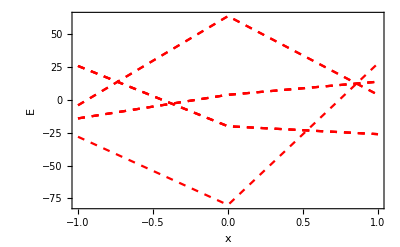

```mathematica
plotLea=Plot[esysStevens[1,x][[1]],{x,-1,1},Frame->True,FrameLabel->{{"E",""},{"x","Stevens Operators"}},PlotStyle->Directive[Red,Dashed]]
```

```mathematica
Max[N[esysStevens[1,0]]]
Min[N[esysStevens[1,0]]]
widthLea=%%-%
```

64.

-80.

144.

Look at eigenvectors at a given value of W and x. The eigenvectors are independent of W and x for J=4.

```mathematica
WVal=1.;
xVal=0.5;
Table[FullSimplify[Normalize[esysStevens[WVal,xVal][[2,idx]]]],{idx,1,Length[esysStevens[WVal,xVal][[2]]]}]
```

{{(√(7/6))/2,0,0,0,-(√(5/3))/2,0,0,0,(√(7/6))/2},{0,0,1/(√2),0,0,0,1/(√2),0,0},{0,0,0,-1/(2 √2),0,0,0,(√(7/2))/2,0},{0,0,-1/(√2),0,0,0,1/(√2),0,0},{0,-(√(7/2))/2,0,0,0,1/(2 √2),0,0,0},{-1/(√2),0,0,0,0,0,0,0,1/(√2)},{0,0,0,(√(7/2))/2,0,0,0,1/(2 √2),0},{0,1/(2 √2),0,0,0,(√(7/2))/2,0,0,0},{(√(5/6))/2,0,0,0,(√(7/3))/2,0,0,0,(√(5/6))/2}}

Derive the formula using group theory. As shown below: simply replacing the real spherical harmonics S[l,m] with the Stevens operators O[l,m] is not correct. Different normalization used. Needs to be investigates further if I want to derive the crystal field expression in terms of Stevens operators for general J and point group symmetry. Since I solved this problem already using the BST operators below (which is physically equivalent), maybe we don’t need that and we just use BST operators. 
Actually, the tutorial on the Hergert website follows exactly the same approach. So maybe it is correct, but I still will use the BST approach for now.

```mathematica
vcrReal=GTCrystalField[Ohgroup,6, GOHarmonics->"Real"]
```

A[0,0] S[0,0]+√(7/5) r^4 A[4,4] S[4,0]+r^4 A[4,4] S[4,4]-(r^6 A[6,4] S[6,0])/(√7)+r^6 A[6,4] S[6,4]

```mathematica
temp=vcrReal/.{S[ll_,mm_]:>GTStevensOperator[ll,mm,JVal]};
%//MatrixForm;
temp=temp/.A[0,0]->0;
matcrA4A6=temp/.{r->1,A[4,4]->a4,A[6,4]->a6};
%//MatrixForm;
Coefficient[matcrA4A6,a4]//MatrixForm
%[[1,1]]/%[[1,5]]
```

(168 √35 | 0 | 0 | 0 | 12 √70 | 0 | 0 | 0 | 0
0 | -252 √35 | 0 | 0 | 0 | 60 √7 | 0 | 0 | 0
0 | 0 | -132 √35 | 0 | 0 | 0 | 180 | 0 | 0
0 | 0 | 0 | 108 √35 | 0 | 0 | 0 | 60 √7 | 0
12 √70 | 0 | 0 | 0 | 216 √35 | 0 | 0 | 0 | 12 √70
0 | 60 √7 | 0 | 0 | 0 | 108 √35 | 0 | 0 | 0
0 | 0 | 180 | 0 | 0 | 0 | -132 √35 | 0 | 0
0 | 0 | 0 | 60 √7 | 0 | 0 | 0 | -252 √35 | 0
0 | 0 | 0 | 0 | 12 √70 | 0 | 0 | 0 | 168 √35)

7 √2

```mathematica
GTStevensOperator[4,0,JVal][[1,1]]/5/GTStevensOperator[4,4,JVal][[1,5]]//FullSimplify
```

√(14/5)

```mathematica
GTStevensOperator[4,0,JVal]+GTStevensOperator[4,4,JVal]//MatrixForm
```

(840 | 0 | 0 | 0 | 12 √70 | 0 | 0 | 0 | 0
0 | -1260 | 0 | 0 | 0 | 60 √7 | 0 | 0 | 0
0 | 0 | -660 | 0 | 0 | 0 | 180 | 0 | 0
0 | 0 | 0 | 540 | 0 | 0 | 0 | 60 √7 | 0
12 √70 | 0 | 0 | 0 | 1080 | 0 | 0 | 0 | 12 √70
0 | 60 √7 | 0 | 0 | 0 | 540 | 0 | 0 | 0
0 | 0 | 180 | 0 | 0 | 0 | -660 | 0 | 0
0 | 0 | 0 | 60 √7 | 0 | 0 | 0 | -1260 | 0
0 | 0 | 0 | 0 | 12 √70 | 0 | 0 | 0 | 840)

```mathematica
Integrate[Sin[θ]*GTTesseralHarmonicY[4,4,θ,ϕ]*Conjugate[GTTesseralHarmonicY[4,4,θ,ϕ]],{θ,0,Pi},{ϕ,0,2*Pi}]
```

1

```mathematica
GTTesseralHarmonicY[4,0,θ,ϕ]
```

(3 (3-30 Cos[θ]^2+35 Cos[θ]^4))/(16 √π)

#### Let’s follow the tutorial on the Hergert website

```mathematica
Clear[m]
vcrReal=GTCrystalField[Ohgroup,6,GOHarmonics->"Real"]/.{A[l_,m_]->B[l,m]/r^l}
%//.{S[l_,m_]:>GTStevensOperator[l,m,JVal]}//Normal;
%/.B[0,0]->0//MatrixForm
```

B[0,0] S[0,0]+√(7/5) B[4,4] S[4,0]+B[4,4] S[4,4]-(B[6,4] S[6,0])/(√7)+B[6,4] S[6,4]

(168 √35 B[4,4]-720 √7 B[6,4] | 0 | 0 | 0 | 12 √70 B[4,4]+360 √70 B[6,4] | 0 | 0 | 0 | 0
0 | -252 √35 B[4,4]+3060 √7 B[6,4] | 0 | 0 | 0 | 60 √7 B[4,4]-180 √7 B[6,4] | 0 | 0 | 0
0 | 0 | -132 √35 B[4,4]-3960 √7 B[6,4] | 0 | 0 | 0 | 180 B[4,4]-2520 B[6,4] | 0 | 0
0 | 0 | 0 | 108 √35 B[4,4]-180 √7 B[6,4] | 0 | 0 | 0 | 60 √7 B[4,4]-180 √7 B[6,4] | 0
12 √70 B[4,4]+360 √70 B[6,4] | 0 | 0 | 0 | 216 √35 B[4,4]+3600 √7 B[6,4] | 0 | 0 | 0 | 12 √70 B[4,4]+360 √70 B[6,4]
0 | 60 √7 B[4,4]-180 √7 B[6,4] | 0 | 0 | 0 | 108 √35 B[4,4]-180 √7 B[6,4] | 0 | 0 | 0
0 | 0 | 180 B[4,4]-2520 B[6,4] | 0 | 0 | 0 | -132 √35 B[4,4]-3960 √7 B[6,4] | 0 | 0
0 | 0 | 0 | 60 √7 B[4,4]-180 √7 B[6,4] | 0 | 0 | 0 | -252 √35 B[4,4]+3060 √7 B[6,4] | 0
0 | 0 | 0 | 0 | 12 √70 B[4,4]+360 √70 B[6,4] | 0 | 0 | 0 | 168 √35 B[4,4]-720 √7 B[6,4])

#### Now let’s use BST operators based on the Y_lm expansion.

Let’s build the crystal field matrix for J=4 in a O_h crystal field.
The coefficient A[0,0] is just a constant (on the diagonal) and can thus be set to zero as it corresponds to an overall shift of spectrum.

```mathematica
vcr
```

A[0,0] Y[0,0]+1/5 r^4 A[4,4] (5 Y[4,-4]+√70 Y[4,0]+5 Y[4,4])+1/7 r^6 A[6,4] (7 Y[6,-4]-√14 Y[6,0]+7 Y[6,4])

```mathematica
temp=vcr/.{Y[ll_,mm_]:>Sqrt[(2*ll+1)/4/Pi]*GTBSTOperator[ll,mm,JVal]}//FullSimplify;
%//MatrixForm;
temp=temp/.A[0,0]->0;
matcrBST=temp/.{r->1,A[4,4]->a4,A[6,4]->a6};
%//MatrixForm
```

((63 √70 a4-45 √182 a6)/(2 √π) | 0 | 0 | 0 | (315 (a4+3 √65 a6))/(2 √π) | 0 | 0 | 0 | 0
0 | (-378 √70 a4+765 √182 a6)/(8 √π) | 0 | 0 | 0 | (315 (2 √5 a4-3 √13 a6))/(4 √(2 π)) | 0 | 0 | 0
0 | 0 | -(99 (√70 a4+5 √182 a6))/(4 √π) | 0 | 0 | 0 | 135/2 (√5 a4-7 √13 a6) √(7/(2 π)) | 0 | 0
0 | 0 | 0 | (162 √70 a4-45 √182 a6)/(8 √π) | 0 | 0 | 0 | (315 (2 √5 a4-3 √13 a6))/(4 √(2 π)) | 0
(315 (a4+3 √65 a6))/(2 √π) | 0 | 0 | 0 | (81 √70 a4+225 √182 a6)/(2 √π) | 0 | 0 | 0 | (315 (a4+3 √65 a6))/(2 √π)
0 | (315 (2 √5 a4-3 √13 a6))/(4 √(2 π)) | 0 | 0 | 0 | (162 √70 a4-45 √182 a6)/(8 √π) | 0 | 0 | 0
0 | 0 | 135/2 (√5 a4-7 √13 a6) √(7/(2 π)) | 0 | 0 | 0 | -(99 (√70 a4+5 √182 a6))/(4 √π) | 0 | 0
0 | 0 | 0 | (315 (2 √5 a4-3 √13 a6))/(4 √(2 π)) | 0 | 0 | 0 | (-378 √70 a4+765 √182 a6)/(8 √π) | 0
0 | 0 | 0 | 0 | (315 (a4+3 √65 a6))/(2 √π) | 0 | 0 | 0 | (63 √70 a4-45 √182 a6)/(2 √π))

```mathematica
temp=vcr/.{Y[ll_,mm_]:>Sqrt[(2*ll+1)/4/Pi]*GTBSTOperator[ll,mm,JVal]}//FullSimplify;
%//MatrixForm;
temp=temp/.A[0,0]->0;
```

```mathematica
$BaseDirectory
SetDirectory[NotebookDirectory[]<>"datasets"];
GTCFDatabaseInfo["CF_Database"];
```

/Library/Mathematica

| Reference | <r^2> | <r^4> | <r^6> | <r^-3>
Ce_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 1.34 | 4.22 | 25.4 | 4.55
Dy_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 0.79 | 1.55 | 6.21 | 9.9
Er_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 0.724 | 1.33 | 5.15 | 11.5
Eu_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 0.925 | 2.06 | 9.11 | 7.69
Gd_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 0.872 | 1.84 | 7.79 | 8.4
Ho_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 0.756 | 1.43 | 5.3 | 10.7
Lu_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 0.65 | 1.11 | 4.2 | 14.1
Nd_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 1.14 | 3.04 | 15.8 | 5.73
Pm_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 1.06 | 2.64 | 13. | 6.35
Pr_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 1.23 | 3.55 | 19.8 | 5.13
Sm_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 0.986 | 2.32 | 10.8 | 7.01
Tb_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 0.829 | 1.68 | 6.91 | 9.14
Tm_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 0.695 | 1.24 | 4.72 | 12.4
Yb_SIC | J. Forstreuter, et al., Phys. Rev. B, 55, 15, 1997 | 0.669 | 1.16 | 4.39 | 13.3

Let’s find the eigenspectrum and eigenvectors as a function of a4 and a6. Obviously, only their ratio should matter. For this, we find the common factor of the matrices multiplying a4 and a6 and pulling that out. Unfortunately, there is no common factor in the matrices multiplying the a4 and a6 coefficients respectively unfortunately.

```mathematica
matA4=Coefficient[matcrBST,a4];
matA6=Coefficient[matcrBST,a6];
a4*matA4+a6*matA6-matcrBST//FullSimplify;
```

```mathematica
temp=matA4;
temp=Abs[Select[Flatten[temp],#≠0&]];
Length[temp];
GCD[temp[[1]],temp[[2]],temp[[3]],temp[[4]],temp[[5]],temp[[6]],temp[[7]],temp[[8]],temp[[9]],temp[[10]],temp[[11]],temp[[12]],temp[[13]],temp[[14]],temp[[15]],temp[[16]],temp[[17]],temp[[18]],temp[[19]]];
(*temp=Table[temp[[i,i]],{i,1,Length[temp]}];
GCD[Abs[temp[[1]]],Abs[temp[[2]]],Abs[temp[[3]]],Abs[temp[[4]]],Abs[temp[[5]]],Abs[temp[[6]]],Abs[temp[[7]]],Abs[temp[[8]]],Abs[temp[[9]]]];*)
Min[temp]//N;
Max[temp]//N;
matA4Av=Norm[Eigenvalues[matA4]]/(2*JVal+1);
(*temp=Flatten[matA4];
matA4Av=Norm[temp]/(2*JVal+1);*)
```

```mathematica
temp=matA6;
temp=Abs[Select[Flatten[temp],#≠0&]];
Length[temp];
GCD[temp[[1]],temp[[2]],temp[[3]],temp[[4]],temp[[5]],temp[[6]],temp[[7]],temp[[8]],temp[[9]],temp[[10]],temp[[11]],temp[[12]],temp[[13]],temp[[14]],temp[[15]],temp[[16]],temp[[17]],temp[[18]],temp[[19]]];
(*temp=Table[temp[[i,i]],{i,1,Length[temp]}];
GCD[Abs[temp[[1]]],Abs[temp[[2]]],Abs[temp[[3]]],Abs[temp[[4]]],Abs[temp[[5]]],Abs[temp[[6]]],Abs[temp[[7]]],Abs[temp[[8]]],Abs[temp[[9]]]];*)
temp//N//MatrixForm;
Min[temp]//N;
Max[temp]//N;
matA6Av=Norm[Eigenvalues[matA6]]/(2*JVal+1);
(* temp=Flatten[matA6];
Norm[temp]/(2*JVal+1)*)
```

```mathematica
ham[x_]=x*matA4/matA4Av+(Abs[x]-1)*matA6/matA6Av//Simplify;
energies[x_]:=Sort[Eigenvalues[ham[x]]];
```

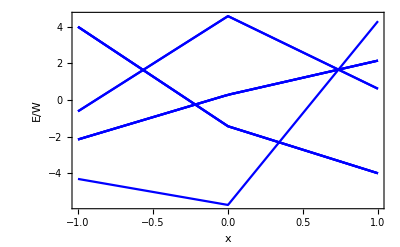

```mathematica
plot1=Plot[energies[x],{x,-1,1},Frame->True,FrameLabel->{{"E/W",""},{"x",""}},PlotStyle->Directive[Blue], FrameStyle->Directive[Thickness[0.0025],FontSize->14,FontFamily->"Helvetica"]]
```

```mathematica
SetDirectory[NotebookDirectory[]~~"../Notes_Peter/Graphics"]
Export["Energies-J_15_2-B_0-BST.pdf",plot1]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/Notes_Peter/Graphics

Energies-J_15_2-B_0-BST.pdf

```mathematica
widthBST=Max[energies[0]]-Min[energies[0]]//N;
temp1=Sort[-energies[-1]/widthBST*widthLea]//N;
temp2=Sort[N[esysStevens[1,1]][[1]]];
evalRatioAt1=temp1[[1]]/temp2[[1]];

ham2[x_]=x*matA4/matA4Av/evalRatioAt1+(1-Abs[x])*matA6/matA6Av//FullSimplify;
energies2[x_]:=Sort[Eigenvalues[-ham2[-x]]];
```

```mathematica
temp1[[1]]/temp1[[4]];
temp2[[1]]/temp2[[4]]//N;
temp1[[1]]/temp1[[6]];
temp2[[1]]/temp2[[6]]//N;
temp1[[1]]/temp1[[9]];
temp2[[1]]/temp2[[9]]//N;
temp1[[4]]/temp1[[6]];
temp2[[4]]/temp2[[6]]//N;
temp1[[4]]/temp1[[9]];
temp2[[4]]/temp2[[9]]//N;
temp1[[6]]/temp1[[9]];
temp2[[6]]/temp2[[9]]//N;
```

We find that BST and Lea et al. spectra are identical, if we choose the same rescaling of A4 and A6 terms. This can be done by looking at the eigenvalues at x=0, where only A4 contributes, and x=1, where only A6 contributes.

```mathematica
energies1[x_]:=Sort[Eigenvalues[-ham[-x]]];
```

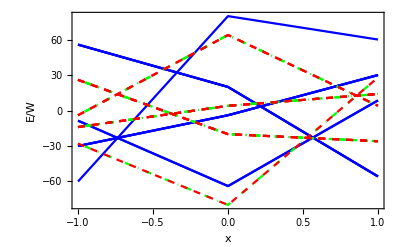

```mathematica
plotBSTScaled=Plot[(energies1[x])/widthBST*widthLea,{x,-1,1},Frame->True,FrameLabel->{{"E",""},{"x","BST (scaled) and Lea energies"}},PlotStyle->Directive[Blue]];
plotBSTScaled2=Plot[(energies2[x])/widthBST*widthLea,{x,-1,1},Frame->True,FrameLabel->{{"E",""},{"x","BST scaled"}},PlotStyle->Directive[Green,DotDashed]];
plot=Show[{plotBSTScaled,plotBSTScaled2,plotLea},PlotRange->All,FrameLabel->{{"E/W",""},{"x",""}},PlotStyle->Directive[Blue], FrameStyle->Directive[Thickness[0.0025],FontSize->14,FontFamily->"Helvetica"]]
```

```mathematica
SetDirectory[NotebookDirectory[]~~"../Notes_Peter/Graphics"]
Export["Energies-J_15_2-B_0-BST_Stevens_Rescaled.pdf",plot]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/Notes_Peter/Graphics

Energies-J_15_2-B_0-BST_Stevens_Rescaled.pdf

#### Show that BST and Stevens matrices are identical

Show that the Stevens and BST matrices are identical. Take two elements (1,1) and (5,1) of the two Hamiltonians H[W,x] and H[a4,a6] and solve for a4[W,x] and a6[W,x].

```mathematica
eqs={matcrA4A6[[1,1]]==matcrStevens[[1,1]],matcrA4A6[[5,1]]==matcrStevens[[5,1]]}
sol=Solve[eqs,{a4,a6}]//FullSimplify
matcr=matcrA4A6/.sol[[1]]//FullSimplify;
```

{168 √35 a4-720 √7 a6==14 W x+4 W (1-Abs[x]),12 √70 a4+360 √70 a6==√70 W x-6 √70 W (1-Abs[x])}

{{a4→(√(5/7) W ((7+√7) x+(-2+6 √7) (-1+Abs[x])))/(12 (35+√5)),a6→(W (-7 (-35+√35) x+2 (735+√35) (-1+Abs[x])))/(2520 (35+√5))}}

Indeed, the two matrices “matcr” (using BST operators) and “matcrStevens” (using Stevens operators) are identical if we use the correct parametrization of W and x.

```mathematica
matcr-matcrStevens//FullSimplify//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (77 W (-(√5-5 √7) x+10 (-1+3 √7) (-1+Abs[x])))/(2 (35+√5)) | 0 | 0 | 0 | (11 W (7 (√5-5 √7) x+2 √5 (-1+3 √7) (-1+Abs[x])))/(2 (35+√5)) | 0 | 0 | 0
0 | 0 | (88 W ((√5-5 √7) x+(10-30 √7) (-1+Abs[x])))/(35+√5) | 0 | 0 | 0 | -(22 W (-7 (-35+√35) x+2 √5 (-21+√7) (-1+Abs[x])))/(7 (35+√5)) | 0 | 0
0 | 0 | 0 | (11 W (-(√5-5 √7) x+10 (-1+3 √7) (-1+Abs[x])))/(2 (35+√5)) | 0 | 0 | 0 | (11 W (7 (√5-5 √7) x+2 √5 (-1+3 √7) (-1+Abs[x])))/(2 (35+√5)) | 0
0 | 0 | 0 | 0 | (88 W (-(√5-5 √7) x+10 (-1+3 √7) (-1+Abs[x])))/(35+√5) | 0 | 0 | 0 | 0
0 | (11 W (7 (√5-5 √7) x+2 √5 (-1+3 √7) (-1+Abs[x])))/(2 (35+√5)) | 0 | 0 | 0 | (11 W (-(√5-5 √7) x+10 (-1+3 √7) (-1+Abs[x])))/(2 (35+√5)) | 0 | 0 | 0
0 | 0 | -(22 W (-7 (-35+√35) x+2 √5 (-21+√7) (-1+Abs[x])))/(7 (35+√5)) | 0 | 0 | 0 | (88 W ((√5-5 √7) x+(10-30 √7) (-1+Abs[x])))/(35+√5) | 0 | 0
0 | 0 | 0 | (11 W (7 (√5-5 √7) x+2 √5 (-1+3 √7) (-1+Abs[x])))/(2 (35+√5)) | 0 | 0 | 0 | (77 W (-(√5-5 √7) x+10 (-1+3 √7) (-1+Abs[x])))/(2 (35+√5)) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
esys[W_,x_]=Eigensystem[matcr]//FullSimplify;
```

$Aborted

```mathematica
Plot3D[esys[W,x][[1,1]],{W,-5,5},{x,-1,1}]
```

-Graphics3D-

```mathematica
plot1=Plot[esys[1,x][[1]],{x,-1,1},Frame->True];
```

The energy spectrum of the Hamiltonians (obviously) derived using BST and Stevens operators agree after proper rescaling of a4 and a6 coefficients, as they are identical.

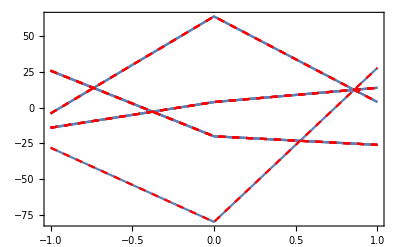

```mathematica
Show[{plot1,plot2}]
```

For J=4, the eigenvectors are independent of W and x.

```mathematica
esys[1,0.5][[2]]
```

{{1,0,0,0,-√(10/7),0,0,0,1},{0,0,1,0,0,0,1,0,0},{0,0,0,-1/(√7),0,0,0,1,0},{0,0,-1,0,0,0,1,0,0},{0,-√7,0,0,0,1,0,0,0},{-1,0,0,0,0,0,0,0,1},{0,0,0,√7,0,0,0,1,0},{0,1/(√7),0,0,0,1,0,0,0},{1,0,0,0,√(14/5),0,0,0,1}}

It is not so easy to take out common factors that are multiplied by a4 and a6 to make them both have the same range. However, one can easily find the minimum and the maximum entries and divide by a number in between the two (or by the min or max to scale the spectrum).

```mathematica
temp=Select[Flatten[Coefficient[matcrA4A6,a4]],#≠0&];
Min[Abs[temp]]
Max[Abs[temp]]
temp=Select[Flatten[Coefficient[matcrA4A6,a6]],#≠0&];
Min[Abs[temp]]
Max[Abs[temp]]
```

105

63 √(35/2)

(45 √(7/2))/2

945 √5

## Training data: O_h=m\bar{3}m symmetry

There are two crystal field parameters {A[4,4], A[6,4]} = {W, x}, where -1 <= x <= 1. Here, W sets the band width of the crystal field spectrum (band width = approx. W/10) and x depends on the ratio of A[4,4] and A[6,4]. We thus draw two random numbers to set W and x. We express energies in Kelvin and thus draw W in the range 10 K - 300 K. This is a rough range of crystal field energies.

```mathematica
WMinVal=1;
WMaxVal=30;
WVal=RandomReal[{WMinVal,WMaxVal}]
xVal=RandomReal[{-1,1}]
```

14.4936

0.734385

### Crystal field Hamiltonian

```mathematica
Ohgroup=GTInstallGroup[Oh,GOVerbose->"False"];
```

```mathematica
vcr=GTCrystalField[Ohgroup,6]
```

A[0,0] Y[0,0]+r^4 A[4,4] Y[4,-4]+√(14/5) r^4 A[4,4] Y[4,0]+r^4 A[4,4] Y[4,4]+r^6 A[6,4] Y[6,-4]-√(2/7) r^6 A[6,4] Y[6,0]+r^6 A[6,4] Y[6,4]

Pr^(3+) has ground state term symbol^3 H_4=^(2S+1)L_J corresponding to S=1, L=5, J=4. Pr 1-2-20 compounds have T_dsymmetry, which has the same CEF expansion as O_h.

```mathematica
JVal=4;
LVal=5;
SVal=1;
gJLS[J_,L_,S_]=1+(J*(J+1)+S*(S+1)-L*(L+1))/(2*J*(J+1));
gVal=gJLS[JVal,LVal,SVal];
```

```mathematica
temp=vcr/.{Y[ll_,mm_]:>Sqrt[(2*ll+1)/4/Pi]*GTBSTOperator[ll,mm,JVal]}//FullSimplify;
%//MatrixForm;
temp=temp/.A[0,0]->0;
matcrBST=temp/.{r->1,A[4,4]->a4,A[6,4]->a6};
%//MatrixForm;
```

```mathematica
matA4=Coefficient[matcrBST,a4];
matA6=Coefficient[matcrBST,a6];
a4*matA4+a6*matA6-matcrBST//FullSimplify;
```

```mathematica
matA4Av=Norm[Eigenvalues[matA4]]/(2*JVal+1);
matA6Av=Norm[Eigenvalues[matA6]]/(2*JVal+1);
```

```mathematica
ham[x_]:=x*matA4/matA4Av+(-1+Abs[x])*matA6/matA6Av//Simplify;
%//MatrixForm;
esys[x_]:=Eigensystem[ham[x]];
```

```mathematica
ham[1.]//MatrixForm
```

(2.15078 | 0. | 0. | 0. | 1.28534 | 0. | 0. | 0. | 0.
0. | -3.22618 | 0. | 0. | 0. | 2.0323 | 0. | 0. | 0.
0. | 0. | -1.6899 | 0. | 0. | 0. | 2.30441 | 0. | 0.
0. | 0. | 0. | 1.38265 | 0. | 0. | 0. | 2.0323 | 0.
1.28534 | 0. | 0. | 0. | 2.76529 | 0. | 0. | 0. | 1.28534
0. | 2.0323 | 0. | 0. | 0. | 1.38265 | 0. | 0. | 0.
0. | 0. | 2.30441 | 0. | 0. | 0. | -1.6899 | 0. | 0.
0. | 0. | 0. | 2.0323 | 0. | 0. | 0. | -3.22618 | 0.
0. | 0. | 0. | 0. | 1.28534 | 0. | 0. | 0. | 2.15078)

Define angular momentum operators {J_x,J_y,J_z}

```mathematica
JVal=4;
JzOp=DiagonalMatrix[Table[-JVal+idx,{idx,0,2*JVal}]];
%//MatrixForm;
JPlusOp=SparseArray[{{i_,j_}->Sqrt[(JVal-(j-JVal-1))*(JVal+(j-JVal-1)+1)]*KroneckerDelta[j,i-1]},{2*JVal+1,2*JVal+1}]//Normal;
%//MatrixForm;
JMinusOp=SparseArray[{{i_,j_}->Sqrt[(JVal+(j-JVal-1))*(JVal-(j-JVal-1)+1)]*KroneckerDelta[j,i+1]},{2*JVal+1,2*JVal+1}]//Normal;
%//MatrixForm;
JxOp=1/2*(JPlusOp+JMinusOp);
%//MatrixForm;
JyOp=-I/2*(JPlusOp-JMinusOp);
%//MatrixForm;
```

Check that my definition of J_z, J_+, J_- agrees with GTBST convention. Note that the order of m_J states is {-J, -J+1, ..., J}. Some BST operators in terms of the angular momentum operators are defined in Table 7.1 on page 166 of Hergert (HG) book.

```mathematica
GTBSTOperator[6,4,JVal]//MatrixForm;
Sqrt[63/512]*1/2*((11*JzOp.JzOp-(JVal*(JVal+1)+38)*IdentityMatrix[2*JVal+1]).JPlusOp.JPlusOp.JPlusOp.JPlusOp+JPlusOp.JPlusOp.JPlusOp.JPlusOp.(11*JzOp.JzOp-(JVal*(JVal+1)+38)*IdentityMatrix[2*JVal+1]))//MatrixForm;

GTBSTOperator[4,4,JVal]//MatrixForm;
Sqrt[35/128]*JPlusOp.JPlusOp.JPlusOp.JPlusOp//MatrixForm;
```

Define function that converts Mathematica expression into Python string

```mathematica
ConvertToPyString[sstr_]:=Module[{str=sstr},
str=Expand[Simplify[str]];
str=N[str];
str=ToString[str,FortranForm];
str=StringReplace[str,Shortest["Sqrt("~~i__~~")"]->"np.sqrt("~~i~~")"];
str=StringReplace[str,Shortest["Abs("~~i__~~")"]->"np.abs("~~i~~")"];
str
]
```

Write python module file that sets up expression of crystal field matrix

```mathematica
outdir=NotebookDirectory[]<>"Input_ham_cr/";
strm=OpenWrite[outdir<>"ham_cr.py"];

SetOptions[strm,FormatType->OutputForm];
SetOptions[strm,PageWidth->Infinity];

pointGroup="Oh";
varsString={"x0","x1"};

Write[strm,"# Module creates crystal field Hamiltonian matrix for point group (PG) Oh and J=4.\n# Number of crystal field variables is 2: {x0, x1}."]
Write[strm,"import numpy as np"]
Write[strm, "def ham_cr_PG_"<>pointGroup<>"_J_"<>ToString[JVal]<>"("<>varsString[[1]]<>", "<>varsString[[2]]<>"):"]
Write[strm,"\t"<>"J = 4"];
Write[strm,"\t"<>"dim=2*J+1"];
Write[strm,"\t"<>"ham = np.arange(dim*dim, dtype=np.float)"];
Write[strm,"\t"<>"ham = ham.reshape(dim,dim)"];
For[idx=0,idx<Length[ham[x]],
For[jdx=0,jdx<Length[ham[x]],
tmp=ConvertToPyString[x0*ham[x1][[idx+1,jdx+1]]];
Write[strm,"\t"<>"ham["<>ToString[idx]<>"]["<>ToString[jdx]<>"] = "<>tmp];
jdx++;
];
idx++;
]
Write[strm,"\t"<>"return ham"];
(*
For [index=1,index≤Length[Flatten[ham[x]]],
label = "# Element "<>ToString[index - 1] <>"\n";
tmp=ConvertToPyString[W*ham[x]]"\n";
Write[strm, label];
Write[strm, tmp];
index++
];
*)
Close[strm]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles/Input_ham_cr/ham_cr.py

Energy spectrum as a function of crystal field parameter x (setting W = 1).

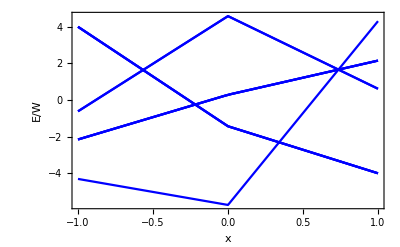

```mathematica
plot1=Plot[Sort[esys[x][[1]]],{x,-1,1},Frame->True,FrameLabel->{{"E/W",""},{"x",""}},PlotStyle->Directive[Blue], FrameStyle->Directive[Thickness[0.0025],FontSize->14,FontFamily->"Helvetica"]]
```

```mathematica
(*SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/Energies-J_4-B_0-BST.pdf", plot1]
*)
```

For a random choice of W and x we find the level spectrum and associated partition function (at B=0). Find numerical eigenvalues (with lowest one set to zero) and eigenstates for that W and x: called energies and evecs.

```mathematica
WVal=4.25
xVal=-0.32(*-0.32*)
```

4.25

-0.32

```mathematica
temp=WVal*esys[xVal][[1]];
energies=temp-Min[temp];
evecs=esys[xVal][[2]];
Zcr[Temp_]:=Sum[Exp[-energies[[i]]/Temp],{i,1,Length[energies]}];
```

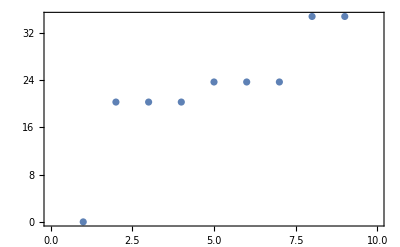

```mathematica
plot1=ListPlot[Sort[energies],Frame->True,PlotRange->{{0,10},Automatic}]
```

Magnetic Jz expectation values of the different levels

```mathematica
WVal*esys[xVal][[1]]-Min[WVal*esys[xVal][[1]]]//Chop
Table[Conjugate[Normalize[esys[xVal][[2,i]]]].JzOp.Normalize[esys[xVal][[2,i]]],{i,1,2*JVal+1}]//Chop
```

{0,34.7739,34.7739,20.2848,20.2848,20.2848,23.6822,23.6822,23.6822}

{0,0,0,-0.5,0.5,0,0,-2.5,2.5}

```mathematica
WVal*esys[xVal][[1]]-Min[WVal*esys[xVal][[1]]]//Chop
esys[xVal][[2,1]]
```

{0,34.7739,34.7739,20.2848,20.2848,20.2848,23.6822,23.6822,23.6822}

{0.456435,0.,0.,0.,0.763763,0.,0.,0.,0.456435}

### Specific heat

Specific heat cV/kB. Enter energies and Temperature (Temp) in Kelvin.

```mathematica
cVOverkB[Temp_]:=1/Temp^2*(1/Zcr[Temp]*Sum[energies[[i]]^2*Exp[-energies[[i]]/Temp],{i,1,Length[energies]}]-(1/Zcr[Temp]*Sum[energies[[i]]*Exp[-energies[[i]]/Temp],{i,1,Length[energies]}])^2);
```

```mathematica
Quiet[maxy=FindMaxValue[{cVOverkB[Temp],Temp>0&&Temp<300},{Temp}]*1.1];
GapAboveGSVal=Select[Table[Sort[energies][[i]]-Sort[energies][[1]],{i,1,Length[energies]-1}],#>0&][[1]];
lineGapAboveGS=Line[{{GapAboveGSVal,0},{GapAboveGSVal,maxy}}];
```

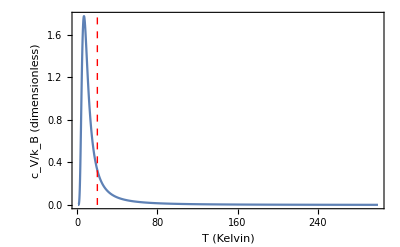

```mathematica
plot1=Plot[cVOverkB[Temp],{Temp,1,300},Frame->True,PlotRange->All,FrameLabel->{{"c_V/k_B (dimensionless)",""},{"T (Kelvin)",""}},Epilog->{Directive[Dashed, Red],lineGapAboveGS},FrameStyle->Directive[Thickness[0.0025],FontSize->14,FontFamily->"Helvetica"]]
```

```mathematica
(*SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/cV-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]*)
```

### Magnetization in finite magnetic field and magnetic susceptibility

```mathematica
Entity["PhysicalConstant","BoltzmannConstant"]["Value"];
Entity["PhysicalConstant","BohrMagneton"]["Value"];
%/%%;
```

```mathematica
263/6.51
```

40.3994

```mathematica
kBVal=1380649/100000000000000000000000000000;
μBVal=9.2740100783000004424165405042207403`9.219079536512577*^-24;
μBVal/kBVal
```

0.671713816

#### Magnetic field along z

```mathematica
hamB[Bfield_,W_,x_]:=W*ham[x]-gJLS[JVal,LVal,SVal]*μBVal/kBVal*JzOp*Bfield//Simplify;
%//MatrixForm;
```

```mathematica
esysB[Bfield_,W_,x_]:=Eigensystem[hamB[Bfield,W,x]];

ZB[Bfield_,Temp_]:=Sum[Exp[-(esysB[Bfield,WVal,xVal][[1,i]]-Min[esysB[Bfield,WVal,xVal][[1]]])/Temp],{i,1,2*JVal+1}];
```

```mathematica
gJLS[JVal,LVal,SVal]*μBVal/kBVal*JzOp*1//MatrixForm;
```

```mathematica
esysB[1,1,-0.32][[1]]
Sort[%-Min[%]]
```

{-5.66313,3.60904,3.30107,1.84303,-1.45024,-0.956386,-0.790818,0.187404,-0.0799633}

{0.,4.21289,4.70675,4.87232,5.58317,5.85054,7.50617,8.96421,9.27217}

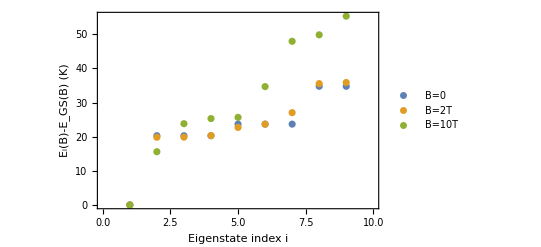

```mathematica
plot1=ListPlot[{Sort[esysB[0,WVal,xVal][[1]]-Min[esysB[0,WVal,xVal][[1]]]],Sort[esysB[2,WVal,xVal][[1]]-Min[esysB[2,WVal,xVal][[1]]]],Sort[esysB[10,WVal,xVal][[1]]-Min[esysB[10,WVal,xVal][[1]]]]},Frame->True,FrameLabel->{{"E_i(B)-E_GS(B)  (K)",""},{"Eigenstate index i",""}},FrameStyle->Directive[Thickness[0.0025],FontSize->14,FontFamily->"Helvetica"],PlotRange->{{0,10},Automatic},PlotLegends->Placed[{"B=0", "B=2T", "B=10T"},Above]]
```

```mathematica
(*SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/Spectrum_Vs_B-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]*)
```

```mathematica
WVal=4.25
xVal=1
BminVal=0.001
```

4.25

1

0.001

```mathematica
esysB[BminVal,WVal,xVal][[1]]
Table[Conjugate[esysB[BminVal,WVal,xVal][[2,i]]].JzOp.esysB[BminVal,WVal,xVal][[2,i]],{i,1,2*JVal+1}]
```

{18.2817,-16.9772,-16.9758,-16.9745,9.1411,9.14083,9.14057,2.61167,2.61167}

{-0.00078384,2.50007,0.000219475,-2.49993,-0.500072,-0.000752486,0.499928,-0.000219475,0.00153633}

```mathematica
Table[Conjugate[esys[xVal][[2,i]]].JzOp.esys[xVal][[2,i]],{i,1,2*JVal+1}]
```

{0,20/7,0,-20,0,-4,4/7,0,0}

{18.2817,-16.9758,-16.9758,-16.9758,9.14083,9.14083,9.14083,2.61167,2.61167}

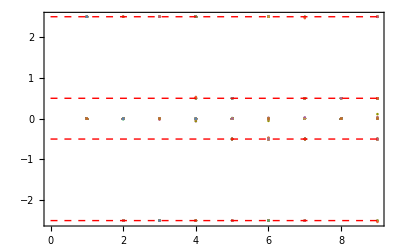

```mathematica
WVal*esys[xVal][[1]]
(*ListPlot[Table[Table[Chop[Conjugate[esys[xVal][[2,i]]].JzOp.esys[xVal][[2,i]]],{i,1,2*JVal+1}],{xVal,-1,1,0.01}]]*)
plot=ListPlot[Table[Table[Conjugate[esysB[BminVal,WVal,xVal][[2,i]]].JzOp.esysB[BminVal,WVal,xVal][[2,i]],{i,1,2*JVal+1}],{xVal,-1,1,0.01}], Epilog->{Directive[Dashed,Red],Line[{{0,-2.5},{9,-2.5}}],Line[{{0,2.5},{9,2.5}}],Line[{{0,-0.5},{9,-0.5}}],Line[{{0,0.5},{9,0.5}}]},Frame->True]
```

Magnetization in finite field

```mathematica
magZ[Bfield_,Temp_]:=1/ZB[Bfield,Temp]*Sum[Conjugate[esysB[Bfield,WVal,xVal][[2,i]]].JzOp.esysB[Bfield,WVal,xVal][[2,i]] *Exp[-(esysB[Bfield,WVal,xVal][[1,i]]-Min[esysB[Bfield,WVal,xVal][[1]]])/Temp],{i,1,2*JVal+1}];
```

```mathematica
Total[Table[Conjugate[esysB[1,WVal,xVal][[2,i]]].JzOp.esysB[1,WVal,xVal][[2,i]]*Exp[-(esysB[1,WVal,xVal][[1,i]]-Min[esysB[1,WVal,xVal][[1]]]) /1],{i,1,2*JVal+1}]]
```

2.45982

```mathematica
plot1=Plot[{magZ[B,1],magZ[B,6.69],magZ[B,44.8],magZ[B,300]},{B,0,10},Frame->True,FrameLabel->{{"M_z/(μ_Bg_J)",""},{"B (T)",""}},PlotLegends->Placed[{"T=1K","T=50K","T=100K","T=300K"},Above]]
```

$Aborted

```mathematica
(*SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/MagnetizationZ_Vs_B-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]*)
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/MagnetizationZ_Vs_B-J_4-W_4.24949-x_-0.320115.pdf

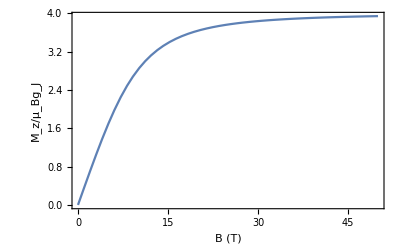

```mathematica
plot1=Plot[{magZ[B,1]},{B,0,50},Frame->True,FrameLabel->{{"M_z/μ_Bg_J",""},{"B (T)",""}},PlotLegends->"Expressions"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/MagnetizationZ_Vs_B-Larger_B-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/MagnetizationZ_Vs_B-Larger_B-J_4-W_4.24949-x_-0.320115.pdf

Susceptibility

```mathematica
BfieldVal=0.001;
chiZ[Temp_]:=gVal*μBVal*magZ[BfieldVal,Temp]/BfieldVal;
```

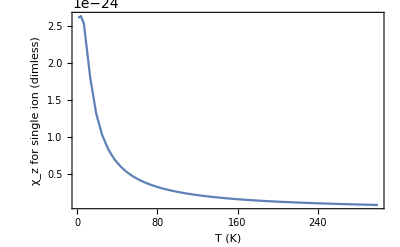

```mathematica
plot2=Plot[chiZ[Temp],{Temp,1,300},Frame->True,FrameLabel->{{"χ_z for single ion (dimless)",""},{"T (K)",""}},PlotRange->All]
```

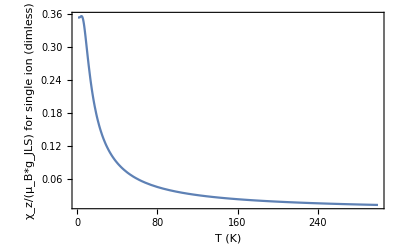

```mathematica
plot2=Plot[chiZ[Temp]/gVal/μBVal,{Temp,1,300},Frame->True,FrameLabel->{{"χ_z/(μ_B*g_JLS) for single ion (dimless)",""},{"T (K)",""}},PlotRange->All]
```

```mathematica
chiZ[15]/gVal/μBVal
```

0.219782

```mathematica
(*SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/SusceptibilityZ_Vs_T-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot2]*)
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/SusceptibilityZ_Vs_T-ZOOM-J_4-W_4.24949-x_-0.320115.pdf

```mathematica
μBVal^2*gVal^2/kBVal*JVal*(JVal+1)
```

7.9737353×10^-23

```mathematica
6*10^23*40*5*10^(-25)
```

12

Check that I am getting the correct van-Vleck susceptibility in the low temperature limit. Important: this requires that the GS be the singlet and I need to use the energy splitting to the triplet with dipole moment 1/2. This depends on the choice of W and x and since these are randomly drawn, the two cells below may not work if the ground state is different or the triplet is not the first excited state (this occurs for x=-0.380623, for which I have checked my calculation).

```mathematica
xVal
```

-0.380623

```mathematica
kBVal/(gJLS[JVal,LVal,SVal]*μBVal)*magZ[0.01,1]/0.01
```

0.127639

```mathematica
40/3/Sort[esysB[0,WVal,xVal][[1]]-Min[esysB[0,WVal,xVal][[1]]]][[2]]
```

0.127639

```mathematica
kBVal/(gJLS[JVal,LVal,SVal]*μBVal)
gJLS[JVal,LVal,SVal]*μBVal
```

1.86091155

7.41920806×10^-24

#### Magnetic field along x

```mathematica
WVal
xVal
```

4.24949

-0.320115

```mathematica
hamBX[Bfield_,W_,x_]:=W*ham[x]-gJLS[JVal,LVal,SVal]*μBVal/kBVal*JxOp*Bfield//Simplify;
%//MatrixForm;
```

```mathematica
esysB[Bfield_,W_,x_]:=Eigensystem[hamBX[Bfield,W,x]];

ZB[Bfield_,Temp_]:=Sum[Exp[-(esysB[Bfield,WVal,xVal][[1,i]]-Min[esysB[Bfield,WVal,xVal][[1]]])/Temp],{i,1,2*JVal+1}];
```

```mathematica
gJLS[JVal,LVal,SVal]*μBVal/kBVal*JzOp*1//MatrixForm;
```

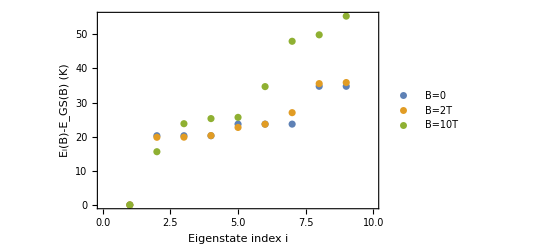

```mathematica
plot2=ListPlot[{Sort[esysB[0,WVal,xVal][[1]]-Min[esysB[0,WVal,xVal][[1]]]],Sort[esysB[2,WVal,xVal][[1]]-Min[esysB[2,WVal,xVal][[1]]]],Sort[esysB[10,WVal,xVal][[1]]-Min[esysB[10,WVal,xVal][[1]]]]},Frame->True,FrameLabel->{{"E_i(B)-E_GS(B)  (K)",""},{"Eigenstate index i",""}},FrameStyle->Directive[Thickness[0.0025],FontSize->14,FontFamily->"Helvetica"],PlotRange->{{0,10},Automatic},PlotLegends->Placed[{"B=0", "B=2T", "B=10T"},Above]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/Spectrum_Vs_BX-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/Spectrum_Vs_BX-J_4-W_4.24949-x_-0.320115.pdf

```mathematica
WVal*esys[xVal][[1]]
Table[Conjugate[esys[xVal][[2,i]]].JzOp.esys[xVal][[2,i]],{i,1,2*JVal+1}]//Chop
```

{-119.224,59.8526,59.8526,-14.7626,-14.7626,-14.7626,14.6021,14.6021,14.6021}

{0,0,0,-0.5,0.5,0,0,-2.5,2.5}

```mathematica
Table[esys[xVal][[2,i]].JzOp.esys[xVal][[2,1]],{i,1,2*JVal+1}]//Chop
Sqrt[20/3]//N
energies[[5]]-energies[[1]]
40/3/%
```

{0,0,0,0,0,-2.58199,0,0,0}

2.58199

104.461

0.127639

Magnetization in finite field

```mathematica
magX[Bfield_,Temp_]:=1/ZB[Bfield,Temp]*Sum[Conjugate[esysB[Bfield,WVal,xVal][[2,i]]].JxOp.esysB[Bfield,WVal,xVal][[2,i]] *Exp[-(esysB[Bfield,WVal,xVal][[1,i]]-Min[esysB[Bfield,WVal,xVal][[1]]])/Temp],{i,1,2*JVal+1}];
```

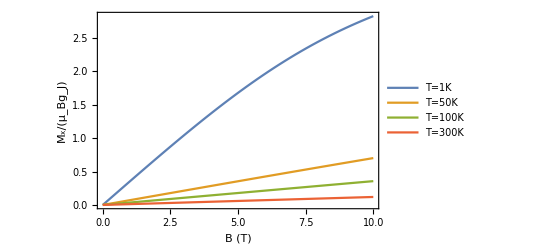

```mathematica
plot1=Plot[{magX[B,1],magX[B,50],magX[B,100],magX[B,300]},{B,0,10},Frame->True,FrameLabel->{{"M_x/(μ_Bg_J)",""},{"B (T)",""}},PlotLegends->Placed[{"T=1K","T=50K","T=100K","T=300K"},Above]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/MagnetizationX_Vs_B-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/MagnetizationZ_Vs_B-J_4-W_4.24949-x_-0.320115.pdf

```mathematica
plot1=Plot[{magX[B,1]},{B,0,50},Frame->True,FrameLabel->{{"M_x/μ_Bg_J",""},{"B (T)",""}},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/MagnetizationX_Vs_B-Larger_B-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/MagnetizationZ_Vs_B-Larger_B-J_4-W_4.24949-x_-0.320115.pdf

Susceptibility

```mathematica
BfieldVal=0.001;
chiX[Temp_]:=gVal*μBVal*magX[BfieldVal,Temp]/BfieldVal;
```

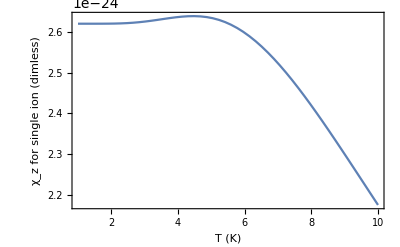

```mathematica
plot2=Plot[chiX[Temp],{Temp,1,300},Frame->True,FrameLabel->{{"χ_x for single ion (dimless)",""},{"T (K)",""}},PlotRange->All]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/SusceptibilityX_Vs_T-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot2]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/SusceptibilityZ_Vs_T-ZOOM-J_4-W_4.24949-x_-0.320115.pdf

```mathematica
μBVal^2*gVal^2/kBVal*JVal*(JVal+1)
```

7.9737353×10^-23

```mathematica
6*10^23*40*5*10^(-25)
```

12

Check that I am getting the correct van-Vleck susceptibility in the low temperature limit. Important: this requires that the GS be the singlet and I need to use the energy splitting to the triplet with dipole moment 1/2. This depends on the choice of W and x and since these are randomly drawn, the two cells below may not work if the ground state is different or the triplet is not the first excited state (this occurs for x=-0.380623, for which I have checked my calculation).

```mathematica
xVal
```

-0.380623

```mathematica
kBVal/(gJLS[JVal,LVal,SVal]*μBVal)*magZ[0.01,1]/0.01
```

0.127639

```mathematica
40/3/Sort[esysB[0,WVal,xVal][[1]]-Min[esysB[0,WVal,xVal][[1]]]][[2]]
```

0.127639

```mathematica
kBVal/(gJLS[JVal,LVal,SVal]*μBVal)
gJLS[JVal,LVal,SVal]*μBVal
```

1.86091155

7.41920806×10^-24

## Training data: C_(4v)= 4mm symmetry

There are two crystal field parameters {A[4,4], A[6,4]} = {W, x}, where -1 <= x <= 1. Here, W sets the band width of the crystal field spectrum (band width = approx. W/10) and x depends on the ratio of A[4,4] and A[6,4]. We thus draw two random numbers to set W and x. We express energies in Kelvin and thus draw W in the range 10 K - 300 K. This is a rough range of crystal field energies.

```mathematica
WMinVal=1;
WMaxVal=30;
WVal=RandomReal[{WMinVal,WMaxVal}]
xVal=RandomReal[{-1,1}]
```

21.6277

0.597848

### Crystal field Hamiltonian

```mathematica
PG=GTInstallGroup[C4v,GOVerbose->"False"];
```

```mathematica
vcr=GTCrystalField[PG,6]
```

A[0,0] Y[0,0]+r^2 A[2,0] Y[2,0]+r^4 A[4,4] Y[4,-4]+r^4 A[4,0] Y[4,0]+r^4 A[4,4] Y[4,4]+r^6 A[6,4] Y[6,-4]+r^6 A[6,0] Y[6,0]+r^6 A[6,4] Y[6,4]

Pr^(3+) has ground state term symbol^3 H_4=^(2S+1)L_J corresponding to S=1, L=5, J=4. Pr 1-2-20 compounds have T_dsymmetry, which has the same CEF expansion as O_h.

```mathematica
JVal=4;
LVal=5;
SVal=1;
gJLS[J_,L_,S_]=1+(J*(J+1)+S*(S+1)-L*(L+1))/(2*J*(J+1));
gVal=gJLS[JVal,LVal,SVal];
```

```mathematica
temp=vcr/.{Y[ll_,mm_]:>Sqrt[(2*ll+1)/4/Pi]*GTBSTOperator[ll,mm,JVal]}//FullSimplify;
%//MatrixForm;
temp=temp/.A[0,0]->0;
matcrBST=temp/.{r->1};
%//MatrixForm;
```

```mathematica
matA20=Coefficient[matcrBST,A[2,0]];
matA44=Coefficient[matcrBST,A[4,4]];
matA40=Coefficient[matcrBST,A[4,0]];
matA64=Coefficient[matcrBST,A[6,4]];
matA60=Coefficient[matcrBST,A[6,0]];
A[2,0]*matA20+A[4,4]*matA44+A[4,0]*matA40+A[6,4]*matA64+A[6,0]*matA60+-matcrBST//FullSimplify;
```

```mathematica
matA20Av=Norm[Eigenvalues[matA20]]/(2*JVal+1);
matA44Av=Norm[Eigenvalues[matA44]]/(2*JVal+1);
matA40Av=Norm[Eigenvalues[matA40]]/(2*JVal+1);matA64Av=Norm[Eigenvalues[matA64]]/(2*JVal+1);matA60Av=Norm[Eigenvalues[matA60]]/(2*JVal+1);
```

```mathematica
ham[x0_,x1_,x2_,x3_,x4_]:=x0*(x1*matA20/matA20Av+x2*matA44/matA44Av+x3*matA40/matA40Av+x4*matA64/matA64Av+(1-Abs[x1]-Abs[x2]-Abs[x3]-Abs[x4])*matA60/matA60Av)//Simplify;
%//MatrixForm;
esys[x0_,x1_,x2_,x3_,x4_]:=Eigensystem[ham[x0,x1,x2,x3,x4]];
```

```mathematica
ham[1.,1,1,1,1]//MatrixForm
```

(5.17526 | 0. | 0. | 0. | 5.82885 | 0. | 0. | 0. | 0.
0. | 7.28779 | 0. | 0. | 0. | 2.54165 | 0. | 0. | 0.
0. | 0. | -16.9293 | 0. | 0. | 0. | 0.359202 | 0. | 0.
0. | 0. | 0. | -1.70246 | 0. | 0. | 0. | 2.54165 | 0.
5.82885 | 0. | 0. | 0. | 12.3374 | 0. | 0. | 0. | 5.82885
0. | 2.54165 | 0. | 0. | 0. | -1.70246 | 0. | 0. | 0.
0. | 0. | 0.359202 | 0. | 0. | 0. | -16.9293 | 0. | 0.
0. | 0. | 0. | 2.54165 | 0. | 0. | 0. | 7.28779 | 0.
0. | 0. | 0. | 0. | 5.82885 | 0. | 0. | 0. | 5.17526)

Define angular momentum operators {J_x,J_y,J_z}

```mathematica
JVal=4;
JzOp=DiagonalMatrix[Table[-JVal+idx,{idx,0,2*JVal}]];
%//MatrixForm;
JPlusOp=SparseArray[{{i_,j_}->Sqrt[(JVal-(j-JVal-1))*(JVal+(j-JVal-1)+1)]*KroneckerDelta[j,i-1]},{2*JVal+1,2*JVal+1}]//Normal;
%//MatrixForm;
JMinusOp=SparseArray[{{i_,j_}->Sqrt[(JVal+(j-JVal-1))*(JVal-(j-JVal-1)+1)]*KroneckerDelta[j,i+1]},{2*JVal+1,2*JVal+1}]//Normal;
%//MatrixForm;
JxOp=1/2*(JPlusOp+JMinusOp);
%//MatrixForm;
JyOp=-I/2*(JPlusOp-JMinusOp);
%//MatrixForm;
```

Check that my definition of J_z, J_+, J_- agrees with GTBST convention. Note that the order of m_J states is {-J, -J+1, ..., J}. Some BST operators in terms of the angular momentum operators are defined in Table 7.1 on page 166 of Hergert (HG) book.

```mathematica
GTBSTOperator[6,4,JVal]//MatrixForm;
Sqrt[63/512]*1/2*((11*JzOp.JzOp-(JVal*(JVal+1)+38)*IdentityMatrix[2*JVal+1]).JPlusOp.JPlusOp.JPlusOp.JPlusOp+JPlusOp.JPlusOp.JPlusOp.JPlusOp.(11*JzOp.JzOp-(JVal*(JVal+1)+38)*IdentityMatrix[2*JVal+1]))//MatrixForm;

GTBSTOperator[4,4,JVal]//MatrixForm;
Sqrt[35/128]*JPlusOp.JPlusOp.JPlusOp.JPlusOp//MatrixForm;
```

Define function that converts Mathematica expression into Python string

```mathematica
ConvertToPyString[sstr_]:=Module[{str=sstr},
str=Expand[Simplify[str]];
str=N[str];
str=ToString[str,FortranForm];
str=StringReplace[str,Shortest["Sqrt("~~i__~~")"]->"np.sqrt("~~i~~")"];
str=StringReplace[str,Shortest["Abs("~~i__~~")"]->"np.abs("~~i~~")"];
str
]
```

Write python module file that sets up expression of crystal field matrix. Use OpenAppend if file exists already. In that case, comment out “import numpy as np” line below.

```mathematica
outdir=NotebookDirectory[]<>"Input_ham_cr/";
(*strm=OpenWrite[outdir<>"ham_cr.py"];*)
strm=OpenAppend[outdir<>"ham_cr.py"];

SetOptions[strm,FormatType->OutputForm];
SetOptions[strm,PageWidth->Infinity];

pointGroup="C4v";
varsString={"x0","x1","x2","x3","x4"};

Write[strm,"# Module creates crystal field Hamiltonian matrix for point group (PG) C4v and J=4.\n# Number of crystal field variables is 5: {x0, x1, x2, x3, x4}."]
(*Write[strm,"import numpy as np"]*)
Write[strm, "def ham_cr_PG_"<>pointGroup<>"_J_"<>ToString[JVal]<>"("<>varsString[[1]]<>", "<>varsString[[2]]<>", "<>varsString[[3]]<>", "<>varsString[[4]]<>", "<>varsString[[5]]<>"):"]
Write[strm,"\t"<>"J = 4"];
Write[strm,"\t"<>"dim=2*J+1"];
Write[strm,"\t"<>"ham = np.arange(dim*dim, dtype=np.float)"];
Write[strm,"\t"<>"ham = ham.reshape(dim,dim)"];
For[idx=0,idx<Length[ham[x0,x1,x2,x3,x4]],
For[jdx=0,jdx<Length[ham[x0,x1,x2,x3,x4]],
tmp=ConvertToPyString[ham[x0,x1,x2,x3,x4][[idx+1,jdx+1]]];
Write[strm,"\t"<>"ham["<>ToString[idx]<>"]["<>ToString[jdx]<>"] = "<>tmp];
jdx++;
];
idx++;
]
Write[strm,"\t"<>"return ham"];
(*
For [index=1,index≤Length[Flatten[ham[x]]],
label = "# Element "<>ToString[index - 1] <>"\n";
tmp=ConvertToPyString[W*ham[x]]"\n";
Write[strm, label];
Write[strm, tmp];
index++
];
*)
Close[strm]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles/Input_ham_cr/ham_cr.py

Energy spectrum as a function of crystal field parameter x (setting W = 1).

```mathematica
plot1=Plot[Sort[esys[x][[1]]],{x,-1,1},Frame->True,FrameLabel->{{"E/W",""},{"x",""}},PlotStyle->Directive[Blue], FrameStyle->Directive[Thickness[0.0025],FontSize->14,FontFamily->"Helvetica"]]
```

-Graphics-

```mathematica
(*SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/Energies-J_4-B_0-BST.pdf", plot1]
*)
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/Energies-J_4-B_0-BST.pdf

For a random choice of W and x we find the level spectrum and associated partition function (at B=0). Find numerical eigenvalues (with lowest one set to zero) and eigenstates for that W and x: called energies and evecs.

```mathematica
WVal=4.25
xVal=-0.32(*-0.32*)
```

4.25

-0.32

```mathematica
temp=WVal*esys[xVal][[1]];
energies=temp-Min[temp];
evecs=esys[xVal][[2]];
Zcr[Temp_]:=Sum[Exp[-energies[[i]]/Temp],{i,1,Length[energies]}];
```

```mathematica
plot1=ListPlot[Sort[energies],Frame->True,PlotRange->{{0,10},Automatic}]
```

-Graphics-

Magnetic Jz expectation values of the different levels

```mathematica
WVal*esys[xVal][[1]]-Min[WVal*esys[xVal][[1]]]//Chop
Table[Conjugate[Normalize[esys[xVal][[2,i]]]].JzOp.Normalize[esys[xVal][[2,i]]],{i,1,2*JVal+1}]//Chop
```

{204.038,204.038,0,34.319,34.319,34.319,119.022,119.022,119.022}

{0,0,0,-2.5,2.5,0,0,0.388889,-0.388889}

```mathematica
WVal*esys[xVal][[1]]-Min[WVal*esys[xVal][[1]]]//Chop
esys[xVal][[2,1]]
```

{0,0,0,22.4988,22.4988,16.8936,16.8936,16.8936,9.04619}

{0.,0.,0.,0.353553,0.,0.,0.,-0.935414,0.}

### Specific heat

Specific heat cV/kB. Enter energies and Temperature (Temp) in Kelvin.

```mathematica
cVOverkB[Temp_]:=1/Temp^2*(1/Zcr[Temp]*Sum[energies[[i]]^2*Exp[-energies[[i]]/Temp],{i,1,Length[energies]}]-(1/Zcr[Temp]*Sum[energies[[i]]*Exp[-energies[[i]]/Temp],{i,1,Length[energies]}])^2);
```

```mathematica
Quiet[maxy=FindMaxValue[{cVOverkB[Temp],Temp>0&&Temp<300},{Temp}]*1.1];
GapAboveGSVal=Select[Table[Sort[energies][[i]]-Sort[energies][[1]],{i,1,Length[energies]-1}],#>0&][[1]];
lineGapAboveGS=Line[{{GapAboveGSVal,0},{GapAboveGSVal,maxy}}];
```

```mathematica
plot1=Plot[cVOverkB[Temp],{Temp,1,300},Frame->True,PlotRange->All,FrameLabel->{{"c_V/k_B (dimensionless)",""},{"T (Kelvin)",""}},Epilog->{Directive[Dashed, Red],lineGapAboveGS},FrameStyle->Directive[Thickness[0.0025],FontSize->14,FontFamily->"Helvetica"]]
```

-Graphics-

```mathematica
(*SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/cV-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]*)
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/cV-J_4-W_4.24949-x_-0.320115.pdf

### Magnetization in finite magnetic field and magnetic susceptibility

```mathematica
Entity["PhysicalConstant","BoltzmannConstant"]["Value"];
Entity["PhysicalConstant","BohrMagneton"]["Value"];
%/%%;
```

```mathematica
263/6.51
```

40.3994

```mathematica
kBVal=1380649/100000000000000000000000000000;
μBVal=9.2740100783000004424165405042207403`9.219079536512577*^-24;
μBVal/kBVal
```

0.671713816

#### Magnetic field along z

```mathematica
hamB[Bfield_,W_,x_]:=W*ham[x]-gJLS[JVal,LVal,SVal]*μBVal/kBVal*JzOp*Bfield//Simplify;
%//MatrixForm;
```

```mathematica
esysB[Bfield_,W_,x_]:=Eigensystem[hamB[Bfield,W,x]];

ZB[Bfield_,Temp_]:=Sum[Exp[-(esysB[Bfield,WVal,xVal][[1,i]]-Min[esysB[Bfield,WVal,xVal][[1]]])/Temp],{i,1,2*JVal+1}];
```

```mathematica
gJLS[JVal,LVal,SVal]*μBVal/kBVal*JzOp*1//MatrixForm;
```

```mathematica
esysB[1,1,-0.32][[1]]
Sort[%-Min[%]]
```

{-5.66313,3.60904,3.30107,1.84303,-1.45024,-0.956386,-0.790818,0.187404,-0.0799633}

{0.,4.21289,4.70675,4.87232,5.58317,5.85054,7.50617,8.96421,9.27217}

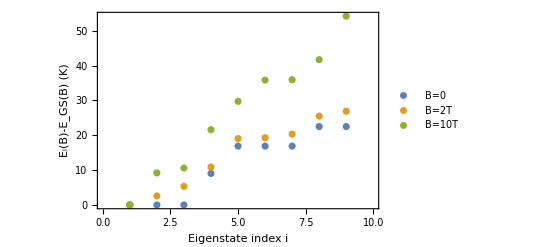

```mathematica
plot1=ListPlot[{Sort[esysB[0,WVal,xVal][[1]]-Min[esysB[0,WVal,xVal][[1]]]],Sort[esysB[2,WVal,xVal][[1]]-Min[esysB[2,WVal,xVal][[1]]]],Sort[esysB[10,WVal,xVal][[1]]-Min[esysB[10,WVal,xVal][[1]]]]},Frame->True,FrameLabel->{{"E_i(B)-E_GS(B)  (K)",""},{"Eigenstate index i",""}},FrameStyle->Directive[Thickness[0.0025],FontSize->14,FontFamily->"Helvetica"],PlotRange->{{0,10},Automatic},PlotLegends->Placed[{"B=0", "B=2T", "B=10T"},Above]]
```

```mathematica
(*SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/Spectrum_Vs_B-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]*)
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/Spectrum_Vs_B-J_4-W_4.24949-x_-0.320115.pdf

```mathematica
WVal=4.25
xVal=1
BminVal=0.001
```

4.25

1

0.001

```mathematica
esysB[BminVal,WVal,xVal][[1]]
Table[Conjugate[esysB[BminVal,WVal,xVal][[2,i]]].JzOp.esysB[BminVal,WVal,xVal][[2,i]],{i,1,2*JVal+1}]
```

{18.2817,-16.9772,-16.9758,-16.9745,9.1411,9.14083,9.14057,2.61167,2.61167}

{-0.00078384,2.50007,0.000219475,-2.49993,-0.500072,-0.000752486,0.499928,-0.000219475,0.00153633}

```mathematica
Table[Conjugate[esys[xVal][[2,i]]].JzOp.esys[xVal][[2,i]],{i,1,2*JVal+1}]
```

{-2.5,6.66134×10^-16,2.5,-6.66134×10^-16,-3.33067×10^-15,0.5,5.10703×10^-15,-0.5,-3.44169×10^-15}

```mathematica
WVal*esys[xVal][[1]]
(*ListPlot[Table[Table[Chop[Conjugate[esys[xVal][[2,i]]].JzOp.esys[xVal][[2,i]]],{i,1,2*JVal+1}],{xVal,-1,1,0.01}]]*)
plot=ListPlot[Table[Table[Conjugate[esysB[BminVal,WVal,xVal][[2,i]]].JzOp.esysB[BminVal,WVal,xVal][[2,i]],{i,1,2*JVal+1}],{xVal,-1,1,0.01}], Epilog->{Directive[Dashed,Red],Line[{{0,-2.5},{9,-2.5}}],Line[{{0,2.5},{9,2.5}}],Line[{{0,-0.5},{9,-0.5}}],Line[{{0,0.5},{9,0.5}}]},Frame->True]
```

{-13.7066,-13.7066,-13.7066,7.66336,7.66336,6.76328,6.76328,6.76328,5.50318}

-Graphics-

Magnetization in finite field

```mathematica
magZ[Bfield_,Temp_]:=1/ZB[Bfield,Temp]*Sum[Conjugate[esysB[Bfield,WVal,xVal][[2,i]]].JzOp.esysB[Bfield,WVal,xVal][[2,i]] *Exp[-(esysB[Bfield,WVal,xVal][[1,i]]-Min[esysB[Bfield,WVal,xVal][[1]]])/Temp],{i,1,2*JVal+1}];
```

```mathematica
Total[Table[Conjugate[esysB[1,WVal,xVal][[2,i]]].JzOp.esysB[1,WVal,xVal][[2,i]]*Exp[-(esysB[1,WVal,xVal][[1,i]]-Min[esysB[1,WVal,xVal][[1]]]) /1],{i,1,2*JVal+1}]]
```

0.352606

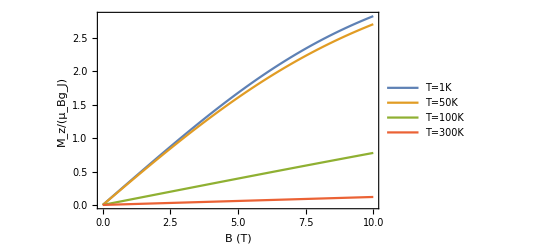

```mathematica
plot1=Plot[{magZ[B,1],magZ[B,6.69],magZ[B,44.8],magZ[B,300]},{B,0,10},Frame->True,FrameLabel->{{"M_z/(μ_Bg_J)",""},{"B (T)",""}},PlotLegends->Placed[{"T=1K","T=50K","T=100K","T=300K"},Above]]
```

```mathematica
(*SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/MagnetizationZ_Vs_B-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]*)
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/MagnetizationZ_Vs_B-J_4-W_4.24949-x_-0.320115.pdf

```mathematica
plot1=Plot[{magZ[B,1]},{B,0,50},Frame->True,FrameLabel->{{"M_z/μ_Bg_J",""},{"B (T)",""}},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/MagnetizationZ_Vs_B-Larger_B-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/MagnetizationZ_Vs_B-Larger_B-J_4-W_4.24949-x_-0.320115.pdf

Susceptibility

```mathematica
BfieldVal=0.001;
chiZ[Temp_]:=gVal*μBVal*magZ[BfieldVal,Temp]/BfieldVal;
```

```mathematica
plot2=Plot[chiZ[Temp],{Temp,1,300},Frame->True,FrameLabel->{{"χ_z for single ion (dimless)",""},{"T (K)",""}},PlotRange->All]
```

-Graphics-

```mathematica
plot2=Plot[chiZ[Temp]/gVal/μBVal,{Temp,1,300},Frame->True,FrameLabel->{{"χ_z/(μ_B*g_JLS) for single ion (dimless)",""},{"T (K)",""}},PlotRange->All]
```

-Graphics-

```mathematica
chiZ[15]/gVal/μBVal
```

0.219782

```mathematica
(*SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/SusceptibilityZ_Vs_T-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot2]*)
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/SusceptibilityZ_Vs_T-ZOOM-J_4-W_4.24949-x_-0.320115.pdf

```mathematica
μBVal^2*gVal^2/kBVal*JVal*(JVal+1)
```

7.9737353×10^-23

```mathematica
6*10^23*40*5*10^(-25)
```

12

Check that I am getting the correct van-Vleck susceptibility in the low temperature limit. Important: this requires that the GS be the singlet and I need to use the energy splitting to the triplet with dipole moment 1/2. This depends on the choice of W and x and since these are randomly drawn, the two cells below may not work if the ground state is different or the triplet is not the first excited state (this occurs for x=-0.380623, for which I have checked my calculation).

```mathematica
xVal
```

-0.380623

```mathematica
kBVal/(gJLS[JVal,LVal,SVal]*μBVal)*magZ[0.01,1]/0.01
```

0.127639

```mathematica
40/3/Sort[esysB[0,WVal,xVal][[1]]-Min[esysB[0,WVal,xVal][[1]]]][[2]]
```

0.127639

```mathematica
kBVal/(gJLS[JVal,LVal,SVal]*μBVal)
gJLS[JVal,LVal,SVal]*μBVal
```

1.86091155

7.41920806×10^-24

#### Magnetic field along x

```mathematica
WVal
xVal
```

4.24949

-0.320115

```mathematica
hamBX[Bfield_,W_,x_]:=W*ham[x]-gJLS[JVal,LVal,SVal]*μBVal/kBVal*JxOp*Bfield//Simplify;
%//MatrixForm;
```

```mathematica
esysB[Bfield_,W_,x_]:=Eigensystem[hamBX[Bfield,W,x]];

ZB[Bfield_,Temp_]:=Sum[Exp[-(esysB[Bfield,WVal,xVal][[1,i]]-Min[esysB[Bfield,WVal,xVal][[1]]])/Temp],{i,1,2*JVal+1}];
```

```mathematica
gJLS[JVal,LVal,SVal]*μBVal/kBVal*JzOp*1//MatrixForm;
```

```mathematica
plot2=ListPlot[{Sort[esysB[0,WVal,xVal][[1]]-Min[esysB[0,WVal,xVal][[1]]]],Sort[esysB[2,WVal,xVal][[1]]-Min[esysB[2,WVal,xVal][[1]]]],Sort[esysB[10,WVal,xVal][[1]]-Min[esysB[10,WVal,xVal][[1]]]]},Frame->True,FrameLabel->{{"E_i(B)-E_GS(B)  (K)",""},{"Eigenstate index i",""}},FrameStyle->Directive[Thickness[0.0025],FontSize->14,FontFamily->"Helvetica"],PlotRange->{{0,10},Automatic},PlotLegends->Placed[{"B=0", "B=2T", "B=10T"},Above]]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/Spectrum_Vs_BX-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/Spectrum_Vs_BX-J_4-W_4.24949-x_-0.320115.pdf

```mathematica
WVal*esys[xVal][[1]]
Table[Conjugate[esys[xVal][[2,i]]].JzOp.esys[xVal][[2,i]],{i,1,2*JVal+1}]//Chop
```

{-119.224,59.8526,59.8526,-14.7626,-14.7626,-14.7626,14.6021,14.6021,14.6021}

{0,0,0,-0.5,0.5,0,0,-2.5,2.5}

```mathematica
Table[esys[xVal][[2,i]].JzOp.esys[xVal][[2,1]],{i,1,2*JVal+1}]//Chop
Sqrt[20/3]//N
energies[[5]]-energies[[1]]
40/3/%
```

{0,0,0,0,0,-2.58199,0,0,0}

2.58199

104.461

0.127639

Magnetization in finite field

```mathematica
magX[Bfield_,Temp_]:=1/ZB[Bfield,Temp]*Sum[Conjugate[esysB[Bfield,WVal,xVal][[2,i]]].JxOp.esysB[Bfield,WVal,xVal][[2,i]] *Exp[-(esysB[Bfield,WVal,xVal][[1,i]]-Min[esysB[Bfield,WVal,xVal][[1]]])/Temp],{i,1,2*JVal+1}];
```

```mathematica
plot1=Plot[{magX[B,1],magX[B,50],magX[B,100],magX[B,300]},{B,0,10},Frame->True,FrameLabel->{{"M_x/(μ_Bg_J)",""},{"B (T)",""}},PlotLegends->Placed[{"T=1K","T=50K","T=100K","T=300K"},Above]]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/MagnetizationX_Vs_B-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/MagnetizationZ_Vs_B-J_4-W_4.24949-x_-0.320115.pdf

```mathematica
plot1=Plot[{magX[B,1]},{B,0,50},Frame->True,FrameLabel->{{"M_x/μ_Bg_J",""},{"B (T)",""}},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/MagnetizationX_Vs_B-Larger_B-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot1]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/MagnetizationZ_Vs_B-Larger_B-J_4-W_4.24949-x_-0.320115.pdf

Susceptibility

```mathematica
BfieldVal=0.001;
chiX[Temp_]:=gVal*μBVal*magX[BfieldVal,Temp]/BfieldVal;
```

```mathematica
plot2=Plot[chiX[Temp],{Temp,1,300},Frame->True,FrameLabel->{{"χ_x for single ion (dimless)",""},{"T (K)",""}},PlotRange->All]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../Notes_Peter/Graphics/SusceptibilityX_Vs_T-J_4-W_"~~ToString[WVal]~~"-x_"~~ToString[xVal]~~".pdf", plot2]
```

/Users/porth/Box/Share with Yuriy Sizyuk/MachineLearning/StevensOperators/MathematicaFiles

../Notes_Peter/Graphics/SusceptibilityZ_Vs_T-ZOOM-J_4-W_4.24949-x_-0.320115.pdf

```mathematica
μBVal^2*gVal^2/kBVal*JVal*(JVal+1)
```

7.9737353×10^-23

```mathematica
6*10^23*40*5*10^(-25)
```

12

Check that I am getting the correct van-Vleck susceptibility in the low temperature limit. Important: this requires that the GS be the singlet and I need to use the energy splitting to the triplet with dipole moment 1/2. This depends on the choice of W and x and since these are randomly drawn, the two cells below may not work if the ground state is different or the triplet is not the first excited state (this occurs for x=-0.380623, for which I have checked my calculation).

```mathematica
xVal
```

-0.380623

```mathematica
kBVal/(gJLS[JVal,LVal,SVal]*μBVal)*magZ[0.01,1]/0.01
```

0.127639

```mathematica
40/3/Sort[esysB[0,WVal,xVal][[1]]-Min[esysB[0,WVal,xVal][[1]]]][[2]]
```

0.127639

```mathematica
kBVal/(gJLS[JVal,LVal,SVal]*μBVal)
gJLS[JVal,LVal,SVal]*μBVal
```

1.86091155

7.41920806×10^-24